```mathematica
`Private`PainleveIINegative["HMMed"] =`HastingsMcLeodMediumNegative`PainleveIIHMMedNeg;
Begin["`HastingsMcLeodMediumNegative`"];
```

## Routine

```mathematica
β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[{σ_,y_},λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[{σ_,y_},λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[{σ_,y_},λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[{σ_,y_},z_]:=Y[{σ,y},z].MatrixExp[(-g[y,z]) σ3];
Φp[{σ_,y_},z_]:=Yp[{σ,y},z].MatrixExp[-(gp[y,z]) σ3];
Φm[{σ_,y_},z_]:=Ym[{σ,y},z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG,S];
S[s_,k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[s_,k_?OddQ]:=({{1, 0}, {s[k], 1}});
GGΣ[_][_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[{s_,y_}][z_]=Φm[{s[1]I,y},z].Inverse[S[s,1]].Inverse[Φm[{s[1]I,y},z]]//Simplify;
GGΣin[{s_,y_}][z_]=GGΣ[y][z]//Inverse;
GG[_,_][_?InfinityQ]:=IdentityMatrix[2];
GG[{s_,y_},6][z_]=Φ[{s[1]I,y},z].S[s,6].Inverse[Φ[{s[1]I,y},z]]//Simplify;
GG[{s_,y_},1][z_]=Φ[{s[1]I,y},z].S[s,1].Inverse[Φ[{s[1]I,y},z]]//Simplify;
GG[{s_,y_},3][z_]=Φ[{s[1]I,y},z].S[s,3].Inverse[Φ[{s[1]I,y},z]]//Simplify;
GG[{s_,y_},4][z_]=Φ[{s[1]I,y},z].S[s,4].Inverse[Φ[{s[1]I,y},z]]//Simplify;
```

```mathematica
GLC[{s_,y_},1][z_]=Inverse[Φm[{s[1]I,y},z]];
GLC[{s_,y_},2][z_]=S[s,6].S[s,1].S[s,3].Inverse[Φ[{s[1]I,y},z]];
GLC[{s_,y_},3][z_]=S[s,6].S[s,1].Inverse[Φp[{s[1]I,y},z]];
```

```mathematica
GRC[{s_,y_},1][z_]=S[s,6].S[s,1].Inverse[Φp[{s[1]I,y},z]];
GRC[{s_,y_},2][z_]=S[s,6].Inverse[Φ[{s[1]I,y},z]];
GRC[{s_,y_},3][z_]=Inverse[Φm[{s[1]I,y},z]];
```

```mathematica
Ψpin[{σ_,y_},z_]=Inverse[Φp[{σ,y},z]];
GMid[{s_,y_}][z_]=Φp[{s[1]I,y},z].S[s,2].Ψpin[{s[1]I,y},z];
```

```mathematica
rngg={.5,2.3};

Cdefs[n_]:={{Function[y,({{-y, y}, {y, -y}})],({{Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})},
{Function[y,({{0}, {Sqrt[y]}})],({{Line[2 {-I,0}], n}, {Line[2 {0,I}], n}})}};
Gl[y_]:={({{GG[y,3], GG[y,6]}, {GG[y,4], GG[y,1]}, {GLC[y,1], GRC[y,1]}, {GLC[y,2], GRC[y,2]}, {GLC[y,3], GRC[y,3]}}),({{GMid[y]}, {GMid[y]}})};
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;

PainleveIIHMMedNeg[sin_,x_]:=Module[{s,y,n},
y=Sqrt[-x/2];
n=25;
{s[1],s[2],s[3]}=sin;
{s[4],s[5],s[6]}=-Array[s,3];
2 ΦθSeries[x]-1/(π I)(Join[ConstructCurve[Cdefs[n],Gl[{s,y}],y],
Fun[GGΣ[{s,y}],Line[{-y+rngg⟦1⟧/y,0,y-rngg⟦1⟧/y}],15]]//RHSolveTop//DomainIntegrate)⟦2⟧
]
```

## Testing

```mathematica
PainleveIIHMMedNeg[{I,2.,-I},-4.99]
```

```mathematica
-1.5779023405968242+5.135270579446303*^-17 ⅈ
```

```mathematica
-1.577902340596824-3.9094317959655727*^-16 ⅈ
```

```mathematica
-1.4112989592446212+4.3070011311485126*^-17 ⅈ
```

```mathematica
-1.2197689218701426-6.051888768895858*^-16 ⅈ
```

```mathematica
-1.0015829871074047-2.8492469021444005*^-16 ⅈ
```

```mathematica
PainleveII[{I,2.,-I},-4.99]
```

```mathematica
-1.5779023378368335-8.13825451473349*^-10 ⅈ
```

```mathematica
-1.4112989592867993-7.613198960143563*^-11 ⅈ
```

```mathematica
-1.2197689219422134+1.1477996331166196*^-10 ⅈ
```

```mathematica
-1.001582987093126-8.029188425240363*^-12 ⅈ
```

```mathematica
x=-2.;y=Sqrt[-x/2];
n=25;
Timing[
2 ΦθSeries[x]-1/(π I)(Join[ConstructCurve[Cdefs[n],Gl[{s,y}],y],
Fun[GGΣ[{s,y}],Line[{-y+rngg⟦1⟧/y,0,y-rngg⟦1⟧/y}],15]]//RHSolveTop//DomainIntegrate)⟦2⟧
]
```

```mathematica
{7.9227189999999155,-1.0015829871074047-2.8492469021444005*^-16 ⅈ}
```

```mathematica
{7.1104980000001206,-1.0015829790469453-1.7338440451033756*^-16 ⅈ}
```

```mathematica
U=Join[ConstructCurve[Cdefs[n],Gl[{s,y}],y],
Fun[GGΣ[{s,y}],Line[{-y+rngg⟦1⟧/y,0,y-rngg⟦1⟧/y}],15]]//RHSolveTop;
```

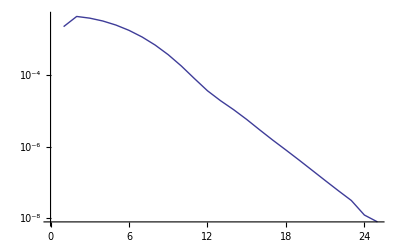
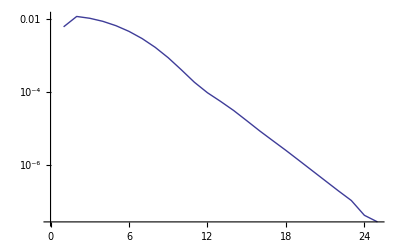
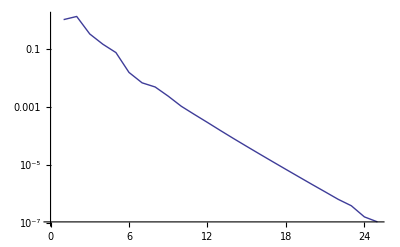
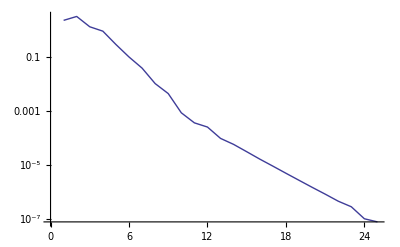
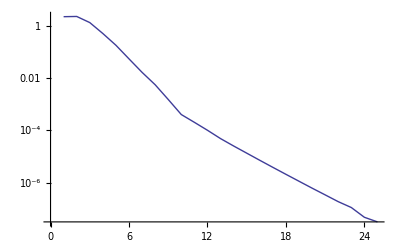
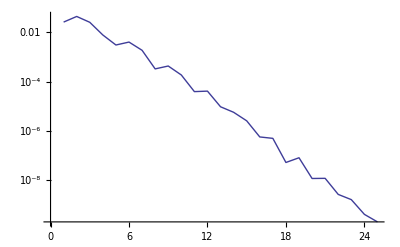
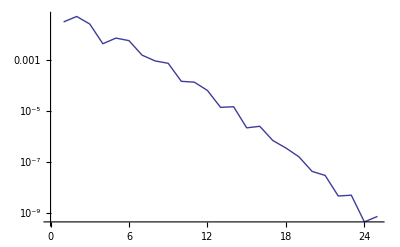
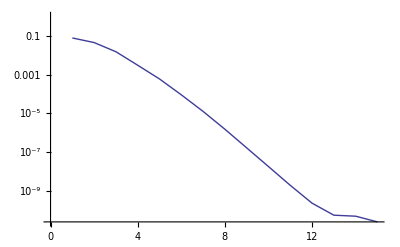
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@U
```

```mathematica
{8.483718000000067,-1.0015829871073305-1.8111491936111694*^-16 ⅈ}
```

```mathematica
{3.3994730000000573,-1.0015829869086945-8.834874115176436*^-18 ⅈ}
```

```mathematica
{10.458356999999978,-1.001582987106026-2.418546789029549*^-16 ⅈ}
```

```mathematica
{16.60514599999999,-1.0015829871059856-3.5118624607826333*^-16 ⅈ}
```

```mathematica
{16.641377000000034,-0.8195182144150668-6.405283733502916*^-17 ⅈ}
```

```mathematica
{13.823225000000093,-0.8195182144163415-4.969616689786745*^-16 ⅈ}
```

```mathematica
{10.928911000000085,-0.8195182144137313-1.766974823035287*^-17 ⅈ}
```

```mathematica
{8.475251999999955,-0.8195182151457234+1.4820501328208472*^-15 ⅈ}
```

```mathematica
{3.494386000000077,-0.8195182094446982-2.6283750492649897*^-16 ⅈ}
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[170,{s[1],s[2],s[3]},x]
```

```mathematica
-1.001582987055197+9.738421180571777*^-11 ⅈ
```

```mathematica
-0.8195182144045465+2.985388325438265*^-11 ⅈ
```

```mathematica
-0.8195182144314473-1.8058193829162406*^-12 ⅈ
```

```mathematica
-0.8195182144243411-1.1749268225003107*^-11 ⅈ
```

```mathematica
-0.8195182144198023-6.912040384499107*^-12 ⅈ
```

## Close

```mathematica
End[]
```